# TP 4 : Restauration d’image

## Travail en séance : Camille LANFREDI & Rémi WEIDLE

Attention, compilez chaque partie séparemment ! Merci !

## Calcul de variations totales

Question 1.

```mathematica
x={{1,2,3},{4,5,6},{7,8,9}}
MatrixForm[x]
x'=MatrixForm[RotateLeft[x]]
x'' = MatrixForm[Transpose[RotateLeft[Transpose[x]]]]
```

{{1,2,3},{4,5,6},{7,8,9}}

(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9)

(4 | 5 | 6
7 | 8 | 9
1 | 2 | 3)

(2 | 3 | 1
5 | 6 | 4
8 | 9 | 7)

Question 2.

```mathematica
variationTotale[x_]:=(Norm[x-RotateLeft[x],"Frobenius"]^2+Norm[x-Transpose[RotateLeft[Transpose[x]]],"Frobenius"]^2)/2
```

Question 3.

```mathematica
(* Constante globale *)
n = 200;
imageUniforme:=RandomReal[1,{n,n}]
Image[imageUniforme]
variationTotale[imageUniforme]
```

-Graphics-

6713.87

La variation totale est de 6700. Ce qui est tres proche de la valeur déterminé dans la préparation qui est de l'ordre de 6500. Le résultat est donc cohérent

Question 4.

```mathematica
image=-Graphics-;
```

```mathematica
mat=ImageData[image]
```

```mathematica
variationTotale[mat]
```

706.62

Pour une image de 200x200, la variation totale est de l'ordre de 1000. Or l'image a une variation totale de 706. Le bruit de l'image et plus faible que celle d'une image uniforme.

Question 5.

```mathematica
σ=0.2;
a0=mat+RandomVariate[NormalDistribution[0,σ],Dimensions[mat]]
```

```mathematica
Image[a0]
variationTotale[a0]
```

-Graphics-

3898.55

Question 6.

Quand nous ajoutons du bruit gaussien dans l'image, nous observons que la valeur de la variation totaleaugmente. Ce qui est cohérent car les valeurs des pixels sont de plus en plus espacés.

## Minimisation par méthode du gradient

```mathematica
(* Constantes globales *)
μ = 0.01;
λ = 10;
```

Question 7.

```mathematica
nextStep[x_]:= x -μ*((4+λ) *x-RotateLeft[x]-Transpose[RotateLeft[Transpose[x]]]-RotateRight[x]-Transpose[RotateRight[Transpose[x]]]-λ*a0)
```

Question 8.

```mathematica
pointsIntermediares = NestList[nextStep,a0,60]
```

Question 9.

```mathematica
Manipulate[Image[pointsIntermediares[[k]]],{k,1,60,1}]
```

Question 10.

```mathematica
Manipulate[{k,variationTotale[pointsIntermediares[[k]]]},{k,1,60,1}]
```

Question 11.

```mathematica
f[x_]:= variationTotale[x]+(λ/2)*Norm[x-a0, "Frobenius"];Manipulate[Abs[f[pointsIntermediares[[k]]]-f[a0]],{k,1,60,1}]
```

Question 12.

```mathematica
μ2 = 0.05;
λ2 = 20;
nextStep2[x_]:= x -μ2*((4+λ2) *x-RotateLeft[x]-Transpose[RotateLeft[Transpose[x]]]-RotateRight[x]-Transpose[RotateRight[Transpose[x]]]-λ2*a0)
pointsIntermediares2 = NestList[nextStep2,a0,60]
```

```mathematica
Manipulate[Image[pointsIntermediares2[[k]]],{k,1,60,1}]
```

```mathematica
Manipulate[variationTotale[pointsIntermediares2[[k]]],{k,1,60,1}]
```

```mathematica
Manipulate[Abs[f[pointsIntermediares2[[k]]]-f[a0]],{k,1,60,1}]
```

La fonction f atteint un minimum local. Cela limite la fonction a une valeur élevée.

## S’il vous reste du temps

Évaluer tout d’abord la cellule suivante.

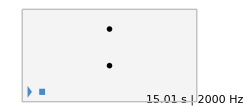

```mathematica
(* fréquence d'échantillonnage *)
freq = 2000;
(* produit une note à la fréquence ξ pendant t secondes *)
note[ξ_,t_]:=Table[Sin[2π ξ k],{k,0.,t,1/freq}];
(* Diverses fréquences *)
D4=293.665;
E4=329.628;
Fsharp4=369.994;
G4=391.995;
A4=440;
(* signal non bruité *)
audio = Flatten[{note[Fsharp4,1], note[Fsharp4,1],note[G4,1], note[A4,1],note[A4,1],note[G4,1],note[Fsharp4,1],note[E4,1],note[D4,1],note[D4,1],note[E4,1],note[Fsharp4,1], note[Fsharp4,3/2],note[E4,1/2],note[E4,1]}];
n = Length[audio];
(* génération du bruit *)
σ=0.1;
bruit=RandomReal[NormalDistribution[0,σ],n];
(* signal à restaurer *)
a0 = audio + bruit;
(* émission du signal *)
Sound[SampledSoundList[a0,freq]]
```

```mathematica
Questions
```

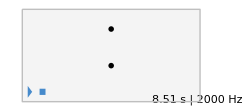

```mathematica
(* Définition de la fonction de coût *)
variationTotaleAudio[x_List] := Total[(x - RotateRight[x])^2];
(* Algorithme de descente de gradient *)
gradientDescent[a0_List, learningRate_, maxIterations_, tolerance_] := Module[{x, xNew, iteration},
  x = a0;
  iteration = 0;
  cost = variationTotaleAudio[x];
  While[iteration < maxIterations,
    gradient = 2*(x - RotateRight[x]);
    xNew = x - learningRate*gradient;
    newCost = variationTotaleAudio[xNew];
    If[Abs[cost - newCost] < tolerance, Break[]];
    x = xNew;
    cost = newCost;
    iteration++;
  ];
  Return[x];
  ];
(* Paramètres *)
learningRate = 0.01;
maxIterations = 150;
tolerance = 1*^-8;
(* Restauration du signal audio *)
restoredSignal = gradientDescent[a0, learningRate, maxIterations, tolerance];
(* Émission du signal restauré *)
Sound[SampledSoundList[restoredSignal, freq]]
```